```mathematica
test[x_,y_,z_]:= Piecewise[{{1, x^2 + y^2 < 1}},z+ x^2 +y^2]
```

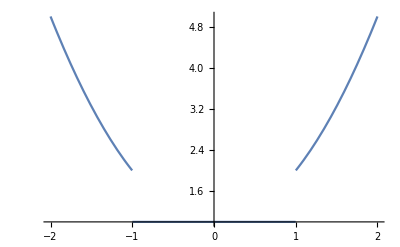

```mathematica
Plot[test[x,0,1],{x,-2,2}]
```

```mathematica
MapThread[test,{{-2,-1,0,1,2},{-2,-1,0,1,2}}]
```

{8,2,1,2,8}

Piecewise::pairs: The first argument {1, False} of Piecewise is not a list of pairs.

Piecewise::pairs: The first argument {1,False} of Piecewise is not a list of pairs.

Piecewise::pairs: The first argument {1,True} of Piecewise is not a list of pairs.

General::stop: Further output of Piecewise::pairs will be suppressed during this calculation.

{Piecewise[{1,(-2)^2+(-2)^2<1},(-2)^2+(-2)^2],Piecewise[{1,(-1)^2+(-1)^2<1},(-1)^2+(-1)^2],Piecewise[{1,0^2+0^2<1},0^2+0^2],Piecewise[{1,1^2+1^2<1},1^2+1^2],Piecewise[{1,2^2+2^2<1},2^2+2^2]}

```mathematica
Outer[test,{1,2,3},{0,1,2},{0,1,2,4}]
```

{{{1,2,3,5},{2,3,4,6},{5,6,7,9}},{{4,5,6,8},{5,6,7,9},{8,9,10,12}},{{9,10,11,13},{10,11,12,14},{13,14,15,17}}}

```mathematica
test[1,1,0]
```

2

```mathematica
Outer[f,{1,2,3},{0,1,2},{0,1,2,4}]
```

{{{f[1,0,0],f[1,0,1],f[1,0,2],f[1,0,4]},{f[1,1,0],f[1,1,1],f[1,1,2],f[1,1,4]},{f[1,2,0],f[1,2,1],f[1,2,2],f[1,2,4]}},{{f[2,0,0],f[2,0,1],f[2,0,2],f[2,0,4]},{f[2,1,0],f[2,1,1],f[2,1,2],f[2,1,4]},{f[2,2,0],f[2,2,1],f[2,2,2],f[2,2,4]}},{{f[3,0,0],f[3,0,1],f[3,0,2],f[3,0,4]},{f[3,1,0],f[3,1,1],f[3,1,2],f[3,1,4]},{f[3,2,0],f[3,2,1],f[3,2,2],f[3,2,4]}}}

```mathematica
Tuples[{{1,2,3},{0,1,2},{0,1,2,4},3}]
```

Tuples::normal: Nonatomic expression expected at position {1,4} in Tuples[{{1,2,3},{0,1,2},{0,1,2,4},3}].

Tuples[{{1,2,3},{0,1,2},{0,1,2,4},3}]

```mathematica
Map[test,Tuples[{-1,0,1},3]]
```

{test[{-1,-1,-1}],test[{-1,-1,0}],test[{-1,-1,1}],test[{-1,0,-1}],test[{-1,0,0}],test[{-1,0,1}],test[{-1,1,-1}],test[{-1,1,0}],test[{-1,1,1}],test[{0,-1,-1}],test[{0,-1,0}],test[{0,-1,1}],test[{0,0,-1}],test[{0,0,0}],test[{0,0,1}],test[{0,1,-1}],test[{0,1,0}],test[{0,1,1}],test[{1,-1,-1}],test[{1,-1,0}],test[{1,-1,1}],test[{1,0,-1}],test[{1,0,0}],test[{1,0,1}],test[{1,1,-1}],test[{1,1,0}],test[{1,1,1}]}

```mathematica
makeTuple[x_,y_,z_]:= {x,y,z}
```

```mathematica
Level[Outer[makeTuple,{1,2,3},{0,1,2},{0,1,2,4}],1]
```

{{{{1,0,0},{1,0,1},{1,0,2},{1,0,4}},{{1,1,0},{1,1,1},{1,1,2},{1,1,4}},{{1,2,0},{1,2,1},{1,2,2},{1,2,4}}},{{{2,0,0},{2,0,1},{2,0,2},{2,0,4}},{{2,1,0},{2,1,1},{2,1,2},{2,1,4}},{{2,2,0},{2,2,1},{2,2,2},{2,2,4}}},{{{3,0,0},{3,0,1},{3,0,2},{3,0,4}},{{3,1,0},{3,1,1},{3,1,2},{3,1,4}},{{3,2,0},{3,2,1},{3,2,2},{3,2,4}}}}

```mathematica
pts = Partition[Flatten[Outer[makeTuple,{1,2,3},{0,1,2},{0,1,2,4}]],3]
val = Flatten[Outer[test,{1,2,3},{0,1,2},{0,1,2,4}]]
```

{{1,0,0},{1,0,1},{1,0,2},{1,0,4},{1,1,0},{1,1,1},{1,1,2},{1,1,4},{1,2,0},{1,2,1},{1,2,2},{1,2,4},{2,0,0},{2,0,1},{2,0,2},{2,0,4},{2,1,0},{2,1,1},{2,1,2},{2,1,4},{2,2,0},{2,2,1},{2,2,2},{2,2,4},{3,0,0},{3,0,1},{3,0,2},{3,0,4},{3,1,0},{3,1,1},{3,1,2},{3,1,4},{3,2,0},{3,2,1},{3,2,2},{3,2,4}}

{1,2,3,5,2,3,4,6,5,6,7,9,4,5,6,8,5,6,7,9,8,9,10,12,9,10,11,13,10,11,12,14,13,14,15,17}

```mathematica
Partition[Flatten[Riffle[pts,val]],4]
```

{{1,0,0,1},{1,0,1,2},{1,0,2,3},{1,0,4,5},{1,1,0,2},{1,1,1,3},{1,1,2,4},{1,1,4,6},{1,2,0,5},{1,2,1,6},{1,2,2,7},{1,2,4,9},{2,0,0,4},{2,0,1,5},{2,0,2,6},{2,0,4,8},{2,1,0,5},{2,1,1,6},{2,1,2,7},{2,1,4,9},{2,2,0,8},{2,2,1,9},{2,2,2,10},{2,2,4,12},{3,0,0,9},{3,0,1,10},{3,0,2,11},{3,0,4,13},{3,1,0,10},{3,1,1,11},{3,1,2,12},{3,1,4,14},{3,2,0,13},{3,2,1,14},{3,2,2,15},{3,2,4,17}}

```mathematica
pts2 = Outer[makeTuple,{1,2,3},{0,1,2},{0,1,2,4}]
val2 = Outer[test,{1,2,3},{0,1,2},{0,1,2,4}];
Riffle[pts2,val2];
```

{{{{1,0,0},{1,0,1},{1,0,2},{1,0,4}},{{1,1,0},{1,1,1},{1,1,2},{1,1,4}},{{1,2,0},{1,2,1},{1,2,2},{1,2,4}}},{{{2,0,0},{2,0,1},{2,0,2},{2,0,4}},{{2,1,0},{2,1,1},{2,1,2},{2,1,4}},{{2,2,0},{2,2,1},{2,2,2},{2,2,4}}},{{{3,0,0},{3,0,1},{3,0,2},{3,0,4}},{{3,1,0},{3,1,1},{3,1,2},{3,1,4}},{{3,2,0},{3,2,1},{3,2,2},{3,2,4}}}}

```mathematica
g[x_,y_,z_]=ϵyz[x,y,z]/.{ϵ0->0.12*((4-5/3)/(15(1-1/3))),a->2,c->(1/4*(4-5/3))};
```

```mathematica
gyz[x_,y_,z_] = Piecewise[{{ϵyz[x,y,z]/.{ϵ0->0.12/Sqrt[3]*((4-5/3)/(15(1-1/3))),a->2,c->(1/4*(4-5/3))},x^2 + y^2 + z^2 > 4.8},{0.05,x^2+y^2 + z^2 ≤ 4}}];
```

```mathematica
pts = Partition[Flatten[Outer[makeTuple,
Range[-10,10,0.2],
Range[-10,10,0.2],
Range[-10,10,0.2]]],3]
```

```mathematica
Flatten[Outer[gyz,Range[-10,10,0.2], Range[-10,10, 0.2], Range[-10,10,0.2]]]
```

{-0.0000949834,-0.0000949331,-0.0000946392,1030296,-0.0000949331,-0.0000949834}
 |  |  |  |